## The pyKraken in the lattice lab

Evaluate full notebook to update plots; choose day via log file (YYY-MM-DD)

```mathematica
path = "/home/pi/Documents/Data Log/Triggered-QPD/";
file = "DataLog_Triggered-QPD_2017-04-24.txt";
tlim={0,24};(*tlim: selection range for triggered measurements *)
```

#### Load data and create plots

```mathematica
(*path = "/home/pi/Git/py2C/";*)
data = Import[path<>file,"CSV"];
trigdata = Select[data,#⟦-1⟧==1&];
(* only triggered *)
```

```mathematica
time=(Flatten@ToExpression@StringSplit[data⟦#1,1⟧,":"]).{1.,1/60,1/3600}&/@Range[1,Length[data]];
trigtime=(Flatten@ToExpression@StringSplit[trigdata⟦#1,1⟧,":"]).{1.,1/60,1/3600}&/@Range[1,Length[trigdata]];
heartbeat=ListPlot[{{time,0 time}ᵀ,{trigtime,0 trigtime}ᵀ},Axes->{Automatic,None},AspectRatio->0.05,ImageSize->700,PlotStyle->PointSize[0.008]];
```

```mathematica
sel=Select[{trigtime,trigdata}ᵀ,tlim⟦1⟧<#⟦1⟧<tlim⟦2⟧&];
trigtime=sel⟦All,1⟧;
trigdata=sel⟦All,2⟧;
```

```mathematica
THcolors={Darker[Gray,0.6],Lighter[Gray,0.6],Darker[Blue,0.6],Lighter[Blue,0.6],Darker[Red,0.6],Lighter[Red,0.6]};
```

```mathematica
THstyles=Directive[THcolors⟦#1⟧,PointSize[0.025]]&/@Range[1,6];
```

```mathematica
pH=ListPlot[{
{time,data⟦All,6⟧}ᵀ,{trigtime,trigdata⟦All,6⟧}ᵀ,
{time,data⟦All,8⟧}ᵀ,{trigtime,trigdata⟦All,8⟧}ᵀ,
{time,data⟦All,10⟧}ᵀ,{trigtime,trigdata⟦All,10⟧}ᵀ
},PlotRange->{{All,All},{All,All}},Joined->{True,False},Frame->True,FrameLabel->{"Time (h)","Rel. humidity (%)"},PlotStyle->THstyles
];
pT=ListPlot[{
{time,data⟦All,7⟧}ᵀ,{trigtime,trigdata⟦All,7⟧}ᵀ,
{time,data⟦All,9⟧}ᵀ,{trigtime,trigdata⟦All,9⟧}ᵀ,
{time,data⟦All,11⟧}ᵀ,{trigtime,trigdata⟦All,11⟧}ᵀ
},PlotRange->{{All,All},{All,All}},Joined->{True,False},Frame->True,FrameLabel->{"Time (h)","Temperature (∘C)"},PlotStyle->THstyles
];
pTH=GraphicsGrid[{{pH,pT}},ImageSize->600];
```

```mathematica
pQPDheap=ListPlot[{trigdata⟦All,{2,3}⟧,trigdata⟦All,{2,3}⟧,trigdata⟦All,{4,5}⟧,trigdata⟦All,{4,5}⟧},PlotRange->All,Frame->True,PlotLabel->"blue/yellow: XDT1, green/red: XDT2",FrameLabel->{"QPD-X (V)","QPD-Y (V)"},PlotStyle->{PointSize[0.04],PointSize[0.01],PointSize[0.04],PointSize[0.01]}];
```

```mathematica
pQPD=ListPlot[{
{trigtime,trigdata⟦All,2⟧}ᵀ,{trigtime,trigdata⟦All,3⟧}ᵀ,{trigtime,trigdata⟦All,4⟧}ᵀ,
{trigtime,trigdata⟦All,5⟧}ᵀ
},PlotRange->{{All,All},{All,All}},Joined->True,Frame->True,FrameLabel->{"Time (h)","V_ADC (V)"}
];
pCorrT=ListPlot[{
{trigdata⟦All,8⟧,trigdata⟦All,2⟧}ᵀ,{trigdata⟦All,8⟧,trigdata⟦All,3⟧}ᵀ,
{trigdata⟦All,8⟧,trigdata⟦All,4⟧}ᵀ,{trigdata⟦All,8⟧,trigdata⟦All,5⟧}ᵀ
},Joined->False,Frame->True,FrameLabel->{"Rel. Humidity (%)", "V_ADC (V)"}];
pCorrH=ListPlot[{
{trigdata⟦All,9⟧,trigdata⟦All,2⟧}ᵀ,{trigdata⟦All,9⟧,trigdata⟦All,3⟧}ᵀ,
{trigdata⟦All,9⟧,trigdata⟦All,4⟧}ᵀ,{trigdata⟦All,9⟧,trigdata⟦All,5⟧}ᵀ
},Joined->False,Frame->True,FrameLabel->{"Temperature (∘C)", "V_ADC (V)"}];
```

```mathematica
Hcorr=LinearModelFit[{trigdata⟦All,8⟧,trigdata⟦All,#1⟧}ᵀ,{1,x},x]&/@{2,3,4,5};
Tcorr=LinearModelFit[{trigdata⟦All,9⟧,trigdata⟦All,#1⟧}ᵀ,{1,x},x]&/@{2,3,4,5};
```

#### Stage data

```mathematica
(* order: XDT1-Y (blue), XDT1-X (yellow), XDT2-X (green), XDT2-Y (red) *)
```

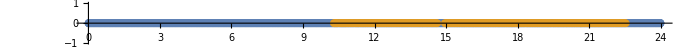

Laser table (black) / Exp table (blue) / above kraken (red)

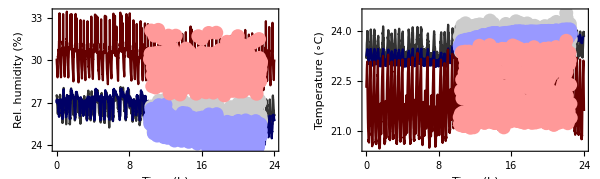

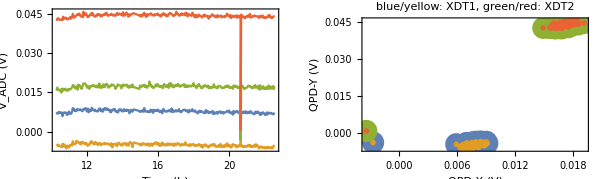

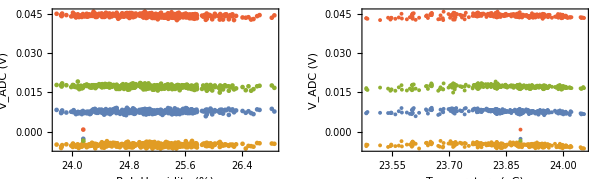

```mathematica
Show[heartbeat]
Print["Laser table (black) / Exp table (blue) / above kraken (red)"]
Show[pTH]
GraphicsGrid[{{pQPD,pQPDheap}},ImageSize->600]
GraphicsGrid[{{pCorrT,pCorrH}},ImageSize->600]
```

```mathematica
{Hcorr⟦#1⟧["ParameterTable"]&/@Range[1,4],
Tcorr⟦#1⟧["ParameterTable"]&/@Range[1,4]}ᵀ//TableForm
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00395644 | 0.0017 | 2.32732 | 0.0205066
x | 0.000148086 | 0.000067686 | 2.18783 | 0.0293296 |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0447424 | 0.00849839 | 5.26481 | 2.42884×10^-7
x | -0.00155513 | 0.000356535 | -4.36179 | 0.0000169039
 | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00549757 | 0.00123348 | -4.45696 | 0.0000111438
x | 0.000018197 | 0.0000491114 | 0.370526 | 0.711211 |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0406754 | 0.00580342 | 7.00887 | 1.20577×10^-11
x | -0.00191796 | 0.000243473 | -7.87752 | 4.06604×10^-14
 | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0213341 | 0.00265945 | 8.02202 | 1.50963×10^-14
x | -0.000168256 | 0.000105887 | -1.58902 | 0.112942 |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0243317 | 0.0135963 | 1.78958 | 0.0743683
x | -0.000303 | 0.000570409 | -0.531197 | 0.595612
 | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0435353 | 0.00512066 | 8.50191 | 5.1642×10^-16
x | 0.0000213015 | 0.000203881 | 0.10448 | 0.916847 |  | Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0589111 | 0.0260859 | 2.25835 | 0.024527
x | -0.00062263 | 0.00109439 | -0.568929 | 0.569762

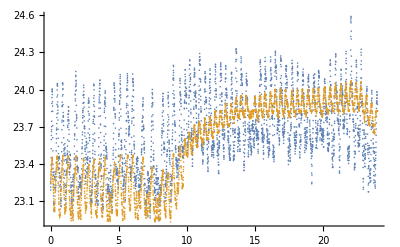

```mathematica
ListPlot[{{time,data⟦All,7⟧}ᵀ,{time,data⟦All,9⟧}ᵀ}]
```